```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["Results/dldw_a1nm_v0.5_b5.5nm_extF2.dat"];
```

```mathematica
data[[3]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,n}
```

{w(au),dlEedwx}

```mathematica
dLEedwx=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,n};
dLHedwx=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,o};
dLEedwy=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,p};
dLHedwy=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,q};
dLEedwz=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,r};
dLHedwz=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,s};
```

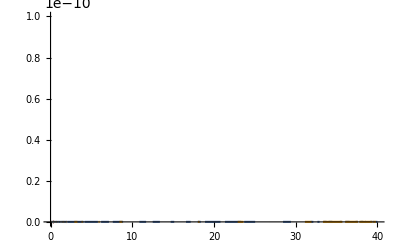

-Graphics-

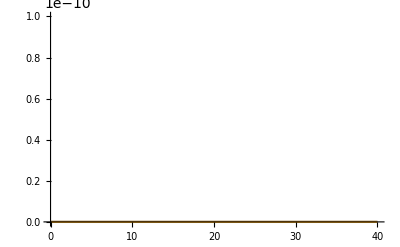

```mathematica
ListPlot[{dLEedwx,dLHedwx}, PlotRange->{{0,40},{0,10^-10}}, Joined->True]
ListPlot[{dLEedwy,dLHedwy}, PlotRange->{{0,40},{0,10^-10}}, Joined->True]
ListPlot[{dLEedwz,dLHedwz}, PlotRange->{{0,40},{0,10^-10}}, Joined->True]
```

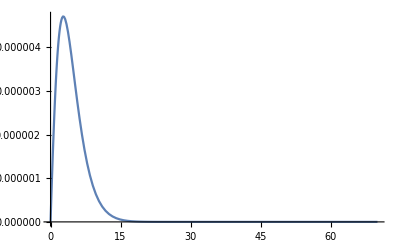

```mathematica
ListPlot[dLHedwx, PlotRange->All, Joined->True]
```

```mathematica
dLHedwx[[700]]
```

{67.5571,0}

```mathematica
dataP=Import["dpdw_a1nm_v0.5_b1.5nm.dat"];
```

```mathematica
dataP[[1]]
```

{w(au),dpEdwx,dpHdwx,dpEdwz,dpHdwz,dpEsdwx,dpHsdwx,dpEsdwz,dpHsdwz,dpEedwx,dpHedwx,dpEedwz,dpHedwz}

```mathematica
dPEedwx=dataP[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_}->{a,j};
dPHedwx=dataP[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_}->{a,k};
```

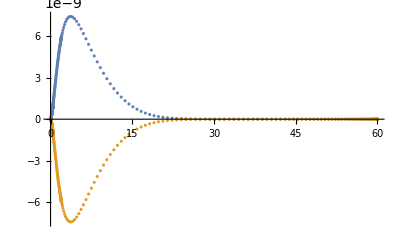

```mathematica
ListPlot[{dPEedwx,dPHedwx}, PlotRange->All]
```

```mathematica
2!!
```

2

```mathematica
II[l_, m_, i1_,i2_]:=Module[{ll=l,mm=m},
If[ll==mm-2||ll==mm-1,0,
If[ll==mm,
If[Mod[i2,2]==0,(-1)^m(2m-1)!!*Beta[(i1+m+2)/2,(i2+1)/2],0],
1/(l-m)((2ll-1)II[ll-1,mm,i1,i2]-(ll+mm-1)II[l-2,m,i1,i2])
]
]
]
```

```mathematica
c=137.035999139;
nm=100./5.2918;
b=1.5*nm;
ω=0.1;
k=ω/c;
v=0.5*c;
γ=1/(√(1-v^2/c^2));
β=v/c;
α[l_,m_]=√((2l+1)/(4π)*((l-m)!)/((l+m)!));
A[l_,m_]:=If[m>=0,1/β^(l+1)∑_(j=m)^l (I^(l-j)(2l+1)!!α[l,m])/(γ^j 2^j(l-j)!((j-m)/2)!((j+m)/2)!)II[l,m,j,l-j],(-1)^Abs[m] A[l,Abs[m]]]
B[l_,m_]:=A[l,m+1] √((l+m+1)(l-m))-A[l,m-1] √((l-m+1)(l+m))
ψE[l_,m_]:=(-2π I^(l-1)k)/(c γ)*B[l,m]/(l(l+1))BesselK[m,(ω*b)/(v*γ)]
ψM[l_,m_]:=(-2π I^(l-1)k*v)/c^2*(m*A[l,m])/(l(l+1))BesselK[m,(ω*b)/(v*γ)]
CC[l_,m_]:=I^l √((2l+1)/(4π)*((l-m)!)/((l+m)!))ψM[l,m]
DD[l_,m_]:=I^l √((2l+1)/(4π)*((l-m)!)/((l+m)!))ψE[l,m]
```

```mathematica
ll1=1;
mm1=-1;
ll2=1;
mm2=-1;
DD[ll1,mm1]*DD[ll2,mm2]*
CC[ll1,mm1]*DD[ll2,mm2]*
DD[ll1,mm1]*CC[ll2,mm2]*
```

4.00589×10^-6+0. ⅈ

-7.70934×10^-7+0. ⅈ

-7.70934×10^-7+0. ⅈ

```mathematica
SphericalBesselJ[1,10]
```

SphericalBesselJ[1,10]

```mathematica
N[SphericalBesselJ[1,10]]
```

0.0784669

```mathematica
II[0,0,0]
```

II[0,0,0]

```mathematica
ll=2;
mm=0;
jj=0.;
II[ll,mm,jj,ll-jj]
```

0.666667

```mathematica
Mod[2,4]
```

2

```mathematica
A[1,0]
```

5.07771+0. ⅈ